## Project 4 Javier Salazar 1001144647.

1.  Industrial Mobility and Peters's Principle.  Suppose a position at a large firm is filled by a person at one of the following  levels : T = trainee, J = junior,  S = senior.  Let  X(t)  denote the level of the person holding a position at time t, and suppose  X(t)  evolves as a Markov process according to the transition rate matrix  Q as follows:

Q = (\ | T | J | S
T | -a_T | a_T | 0
J | a_JT | -a_J | a_JS
S | a_S | 0 | -a_S)   

In words, a trainee stays at the rank for an exponentially distributed time ~ a_T and then becomes a junior.  A junior  stays
at that rank for an exponentially distributed time ~ a_J = a_JT+ a_JS and subsequently will be promoted to a senior with probability a_JS/a_J or the junior leaves the position with probability a_JT/a_Jand will be immediately replaced by a trainee.  A senior stays
at that rank for an exponentially distributed time ~ a_S and then leaves (or gets fired according to the Peter's Principle of reaching the level of incompetence) and will be immediately replaced by a trainee.  Suppose the mean time spent in positions T, J, S  are as follows: 1, 2, 5 years  (- q_ii  = 1/(mean time spent at i) in the matrix Q).  Assume in addition that the chance of  being promoted from J to S is 2/5.

(a)  Find  the transition probability matrix  P(t) = ⅇ^(Q t)

```mathematica
<<BarCharts`
```

GeneralizedBarChart::shdw: Symbol GeneralizedBarChart appears in multiple contexts {BarCharts`,Global`}; definitions in context BarCharts` may shadow or be shadowed by other definitions.

General::obspkg: BarCharts` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Q=({{-1, 1, 0}, {3/10, -1/2, 1/5}, {1/5, 0, -1/5}});
P[t_]:=MatrixExp[Q*t];
P[t]//MatrixForm
```

(1/5+(90 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)+(10 √89 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)-(90 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89)+(10 √89 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89) | 2/5-(130 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)-(10 √89 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)+(130 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89)-(10 √89 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89) | 2/5+(40 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)-(40 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89)
1/5-(31 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)-(3 √89 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)+(31 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89)-(3 √89 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89) | 2/5+(25 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)+(5 √89 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)-(25 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89)+(5 √89 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89) | 2/5+(6 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)-(2 √89 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)-(6 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89)-(2 √89 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89)
1/5-(14 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)-(2 √89 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)+(14 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89)-(2 √89 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89) | 2/5+(40 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)-(40 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89) | 2/5-(26 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)+(2 √89 ⅇ^(-(17 t)/20-(√89 t)/20))/(89+17 √89)+(26 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89)+(2 √89 ⅇ^(-(17 t)/20+(√89 t)/20))/(-89+17 √89))

(b)  Find the stationary distribution π = (π_T, π_J, π_S)  by taking  lim_(t→∞) P(t)  (each row is π)

```mathematica
M=Limit[P[t],t->Infinity];
M//MatrixForm
```

(1/5 | 2/5 | 2/5
1/5 | 2/5 | 2/5
1/5 | 2/5 | 2/5)

```mathematica
(*πT=1/5, πJ=2/5, πS=2/5*)
```

(c)  Find  the stationary distribution  π  by  solving    π Q = O

```mathematica
Solve[{πT,πJ,πS}.Q=={0,0,0},{πT,πJ,πS}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{πJ→2 πT,πS→2 πT}}

```mathematica
(*By linear algebra and inspection the solution is πT=1/5, πJ=2/5, πS=2/5*)
```

2.   Barber Shop.  There are 2 waiting chairs and 2 barbers. Customers arriving to fully occupied shop are turned away.
Assume that customers arrive according to Poisson process at rate of  5/hour (inter arrivals are exponential ~ λ = 5) and 
the service rate is  2/hour (services are exponential ~ μ = 2).  If  X(t) = the number of the customers in the shop at time t,   
then it can be modelled by a birth-death process on states {0, 1, 2 ,3 , 4} with the following transition rate matrix

Q = (-5 | 5 | 0 | 0 | 0
2 | -7 | 5 | 0 | 0
0 | 4 | -9 | 5 | 0
0 | 0 | 4 | -9 | 5
0 | 0 | 0 | 4 | -4)

Suppose that at the time of opening the shop at 8 AM there were 2 customers waiting.

(a)  Using  p(t) = p(0) P(t)  find the probability that the shop will be full at:  9AM, 10AM, 12PM, 4PM

```mathematica
Q=({{-5, 5, 0, 0, 0}, {2, -7, 5, 0, 0}, {0, 4, -9, 5, 0}, {0, 0, 4, -9, 5}, {0, 0, 0, 4, -4}});
P[t_]:=MatrixExp[Q*t];
P[t]//N//MatrixForm;
p[t_]:={0,0,1,0,0}.P[t];
For[i=1,i≤8,i=i*2,Print[p[i]//N]] (*The last entry in the matrix is the probablity that the shop is full at the respective time*)
```

{0.0717358,0.17338,0.207755,0.247386,0.299743}

{0.0658251,0.16359,0.203281,0.252612,0.314692}

{0.0648914,0.162212,0.202746,0.253408,0.316742}

{0.0648758,0.16219,0.202737,0.253421,0.316776}

(b)  Find the stationary distribution π

```mathematica
M=Limit[P[t]//N,t->Infinity];
M//MatrixForm (*Stationary distribution is along the diagonal for each respective state*)
```

(0.0648758 | 0.16219 | 0.202737 | 0.253421 | 0.316776
0.0648758 | 0.16219 | 0.202737 | 0.253421 | 0.316776
0.0648758 | 0.16219 | 0.202737 | 0.253421 | 0.316776
0.0648758 | 0.16219 | 0.202737 | 0.253421 | 0.316776
0.0648758 | 0.16219 | 0.202737 | 0.253421 | 0.316776)

(c)  Assume X(0) = 2.  Simulate  n = 365 days sample (assume the shop operates 8AM - 8PM).
       Compare the frequencies of states to the stationary distribution π.
(d)  Repeat  (c)  for n = 10,000.

```mathematica
Q=({{-5, 5, 0, 0, 0}, {2, -7, 5, 0, 0}, {0, 4, -9, 5, 0}, {0, 0, 4, -9, 5}, {0, 0, 0, 4, -4}});
P[t_]:=MatrixExp[Q*t];
P[t]//N//MatrixForm;
p[t_]:={0,0,1,0,0}.P[t];
p[365*12]//N
p[10000*12]//N
```

General::munfl: Exp[-68542.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-45537.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.0648758,0.16219,0.202737,0.253421,0.316776}

General::munfl: Exp[-1.87789×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.24759×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.0648758,0.16219,0.202737,0.253421,0.316776}

3.  Car Service.   A service is carried out sequentially as follows:  T(tune-up), A(air-conditioning), B(brakes).  The mean 
service times are respectively 1,2,3 hours. Assume the services are independent and exponentially distributed.  If  X(t) denotes
the state of service at time t then it can be modelled by a birth-death process on states {1,2,3,4} where 4 corresponds to the 
absorbing state (i.e., all three services 1-T, 2-A, 3-B have been completed and therefore the transition rate to leave 4 is 0).  
Then the transition rate matrix has the form

 Q = (-1 | 1 | 0 | 0
0 | -1/2 | 1/2 | 0
0 | 0 | -1/3 | 1/3
0 | 0 | 0 | 0)
 
Notice that the transition rate = 1/(mean times spent at a given state).

(a) What is the probability that 5 hours after the service started the car is still in the brake repair stage?

```mathematica
Q=({{-1, 1, 0, 0}, {0, -1/2, 1/2, 0}, {0, 0, -1/3, 1/3}, {0, 0, 0, 0}});
P[t_]:=MatrixExp[Q*t];
P[5]//N//MatrixForm (*0.189*)
```

(0.00673795 | 0.150694 | 0.367537 | 0.475031
0. | 0.082085 | 0.320372 | 0.597543
0. | 0. | 0.188876 | 0.811124
0. | 0. | 0. | 1.)

(b) What is the probability that the service has been completed at the end of the 6-th  hour?

```mathematica
P[6]//N//MatrixForm (*0.864*)
```

(0.00247875 | 0.0946166 | 0.314004 | 0.5889
0. | 0.0497871 | 0.256645 | 0.693568
0. | 0. | 0.135335 | 0.864665
0. | 0. | 0. | 1.)

4.  Linear Growth Model with Immigration.  Let  X(t)  has the parameters  λ_0= λ,  μ_0= μ,   μ_n= n μ ,  λ_n= n λ + θ   for  n ≥ 1 
 and let  λ < μ.   Then the expected population size  m(t) = x_0ⅇ^((λ-μ)t) + θ/(λ-μ)[ ⅇ^((λ-μ)t)- 1 ] →θ/(μ - λ) = equilibrium size, as  t → ∞.
 Let the population of  100  has the birth rate  λ =1 /individual/year, death rate  μ = 1.2 individual/year, and the immigration factor 
  θ = 1 /year.

(a)  Simulate n = 1000 samples of the population size at time t = 30 years, calculate the sample average and compare to m(t).

```mathematica
Table[λp[n_]:=n*1+1,{n,1,1000}];Table[μp[n_]:=n*1.2,{n,1,1000}];
t=30;x0=100;
exactmean:=1/(1.2-1)
TotCust={};
Do[s=0;NumCust= x0;n=NumCust;
Label[start];r=Random[ExponentialDistribution[λp[n]+μp[n]]]; s=s+r;If[s≤t, If[RandomReal[{0,1}]<λp[n]/(λp[n]+μp[n]),NumCust=NumCust+1;
n=NumCust;Goto[start],NumCust=NumCust-1;n=NumCust;Goto[start]]];AppendTo[TotCust,NumCust]
,{1000}]
Print["The average mean is ", Mean[TotCust]//N]
Print["The exact mean is ", exactmean]
```

The average mean is 5.236

The exact mean is 5.

(b)  Calculate probability frequencies of population size at t = 30 for n =1000 samples and graph the frequencies together with
       the stationary distribution for comparison.

1000

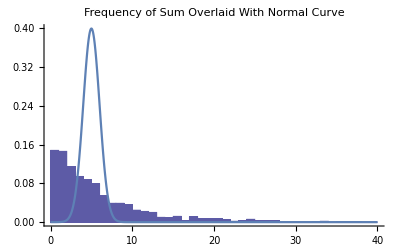

```mathematica
bcount=BinCounts[TotCust,{0,40,1}];
Total[bcount]
Show[GeneralizedBarChart[Table[{.5+(i-1)*1,bcount[[i]]/(1*1000),1},{i,1,40}],PlotLabel->"Frequency of Sum Overlaid With Normal Curve"],Plot[1/√(2*Pi)*Exp[-(x-5)^2/2],{x,0,40},PlotRange->All]]
```

(c)  Graph a single sample of population evolution in 30 years

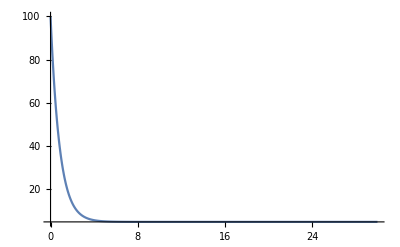

```mathematica
Plot[100*Exp[-1.2*x]-5*(Exp[-1.2*x]-1),{x,0,30},PlotRange->All]
```